```mathematica
z[T_]:=(1/2(EllipticTheta[3,0,Exp[-1/T]]-1))
```

```mathematica
d[T_]:=z[T]^2/z[0.5*T]
```

```mathematica
fb[T_]:=(d[T]+1)/(4*d[T]+2)
```

```mathematica
ff[T_]:=(d[T]-1)/(4*d[T]-2)
```

```mathematica
Wb[T_]:=-2*T*fb[T]*Log[fb[T]]
```

```mathematica
Wf[T_]:=-2*T*ff[T]*Log[ff[T]]
```

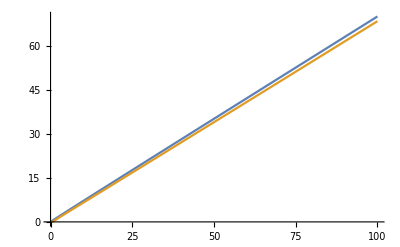

```mathematica
Plot[{Wb[T],Wf[T]},{T,0,100}]
```

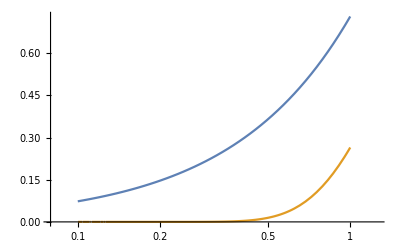

```mathematica
LogLinearPlot[{Wb[T],Wf[T]},{T,0.1,1}]
```

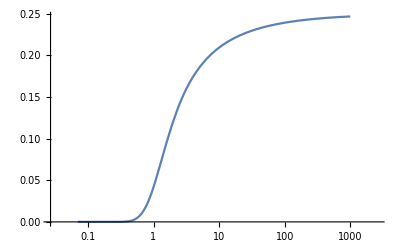

```mathematica
LogLinearPlot[ff[T],{T,0.07,1000}]
```

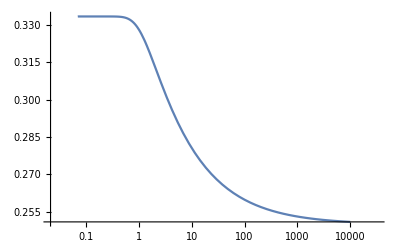

```mathematica
LogLinearPlot[fb[T],{T,0.07,10000}]
```

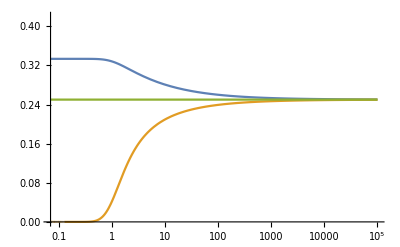

```mathematica
LogLinearPlot[{fb[T],ff[T],0.25},{T,0.07,100000},PlotRange->{{7*10^-2,10^5},{0,0.42}}]
```

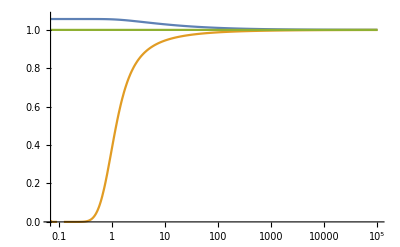

```mathematica
LogLinearPlot[{-2*fb[T]*Log[fb[T]]/Log[2],-2*ff[T]*Log[ff[T]]/Log[2],1},{T,0.07,100000},PlotRange->{{7*10^-2,10^5},{0,1.07}}]
```

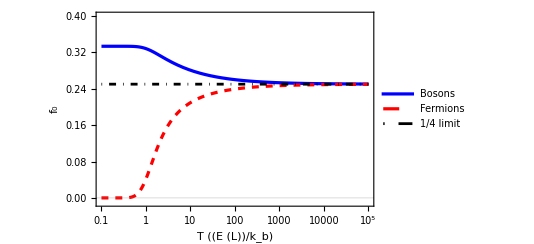

```mathematica
LogLinearPlot[{fb[T],ff[T],0.25},{T,0.1,100000},PlotTheme->"Scientific",PlotRange->{{0.1,100000},{-0.01,0.4}},PlotStyle->{{Blue,AbsoluteThickness[2.3]},{Dashed,Red,AbsoluteThickness[2.3]},{DotDashed,Black,AbsoluteThickness[2.]}},FrameLabel->{{HoldForm[Subscript["f",0]],None},{HoldForm[T " "[("E" "(L)")/Subscript[k, b]]],None}},PlotLabel->None,LabelStyle->{FontFamily->"Latin Modern Roman",15,GrayLevel[0]},PlotLegends->Placed[{"Bosons","Fermions","1/4 limit"},{0.76,0.3}]]
```

```mathematica
Export["Probability_ferm_bose.png",LogLinearPlot[{fb[T],ff[T],0.25},{T,0.1,100000},PlotTheme->"Scientific",PlotRange->{{0.1,100000},{-0.01,0.4}},PlotStyle->{{Blue,AbsoluteThickness[2.3]},{Dashed,Red,AbsoluteThickness[2.3]},{DotDashed,Black,AbsoluteThickness[2.]}},FrameLabel->{{HoldForm[Subscript["f",0]],None},{HoldForm[T " "[("E" "(L)")/Subscript[k, b]]],None}},PlotLabel->None,LabelStyle->{FontFamily->"Latin Modern Roman",15,GrayLevel[0]},PlotLegends->Placed[{"Bosons","Fermions","1/4 limit"},{0.76,0.3}]],ImageResolution->1*160]
```

Probability_ferm_bose.png

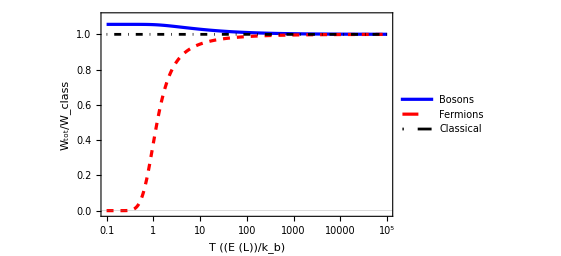

```mathematica
LogLinearPlot[{-(2 fb[T] Log[fb[T]])/Log[2],-(2 ff[T] Log[ff[T]])/Log[2],1},{T,0.1,100000},PlotTheme->"Scientific",PlotRange->{{0.1,100000},{-0.01,1.1}},PlotStyle->{{Blue,AbsoluteThickness[2.3]},{Dashed,Red,AbsoluteThickness[2.3]},{DotDashed,Black,AbsoluteThickness[2.]}},FrameLabel->{{HoldForm[Subscript[W,tot]/Subscript[W, class]],None},{HoldForm[T " "[("E" "(L)")/Subscript[k, b]]],None}},PlotLabel->None,LabelStyle->{FontFamily->"Latin Modern Roman",15,GrayLevel[0]},PlotLegends->Placed[{"Bosons","Fermions","Classical"},{0.76,0.3}]]
```

```mathematica
Export["work_ferm_bose.png",LogLinearPlot[{-(2 fb[T] Log[fb[T]])/Log[2],-(2 ff[T] Log[ff[T]])/Log[2],1},{T,0.1,100000},PlotTheme->"Scientific",PlotRange->{{0.1,100000},{-0.01,1.1}},PlotStyle->{{Blue,AbsoluteThickness[2.3]},{Dashed,Red,AbsoluteThickness[2.3]},{DotDashed,Black,AbsoluteThickness[2.]}},FrameLabel->{{HoldForm[Subscript[W,tot]/Subscript[W, class]],None},{HoldForm[T " "[("E" "(L)")/Subscript[k, b]]],None}},PlotLabel->None,LabelStyle->{FontFamily->"Latin Modern Roman",15,GrayLevel[0]},PlotLegends->Placed[{"Bosons","Fermions","Classical"},{0.76,0.3}]],ImageResolution->1*160]
```

work_ferm_bose.png

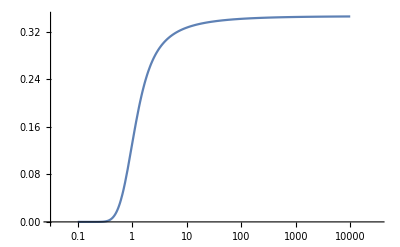

```mathematica
LogLinearPlot[-ff[T]*Log[ff[T]],{T,0.1,10000}, PlotRange->All]
```

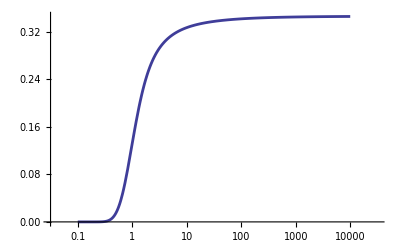

```mathematica
LogLinearPlot[-ff[T] Log[ff[T]],{T,0.1,10000},PlotStyle->Directive[Hue[0.67,0.6,0.6],AbsoluteThickness[2.]],PlotRange->All]
```

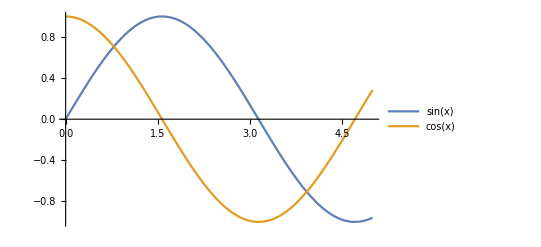

```mathematica
Plot[{Sin[x],Cos[x]},{x,0,5},PlotLegends->LineLegend["Expressions"]]
```

```mathematica
FullSimplify[fb[T]]
```

1/4 (1+(-1+EllipticTheta[3,0,ⅇ^(-2./T)])/(EllipticTheta[3,0,ⅇ^(-2./T)]+(-2+EllipticTheta[3,0,ⅇ^(-1/T)]) EllipticTheta[3,0,ⅇ^(-1/T)]))

```mathematica
FullSimplify[ff[T]]
```

1/4 (1+(-1+EllipticTheta[3,0,ⅇ^(-2./T)])/(-2+EllipticTheta[3,0,ⅇ^(-2./T)]-(-2+EllipticTheta[3,0,ⅇ^(-1/T)]) EllipticTheta[3,0,ⅇ^(-1/T)]))